Pablo Chehade
Ejercicio 1 - 	TP 5

```mathematica
ClearAll["Global`*"]
```

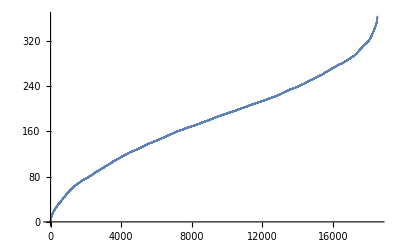

```mathematica
(*importo los datos*)
nombre = "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP 05/Ejercicio 1/Chehade_18500 particulas atrapadas.dat";
datos = Import[nombre, "FieldSeparators"->"\t"];
x = datos⟦All,1⟧;
y = datos⟦All,2⟧;
tiempos = datos⟦All,3⟧;
Nmalla = 1024; 

(*El primer elemento es la semilla*)
(*Calculo la distancia a la semilla: *)

xseed = x⟦1⟧;
yseed = y⟦1⟧;
distancias = ConstantArray[0,Length[x]];
Do[
distancias⟦j⟧=N[√((x⟦j⟧-xseed)^2+(y⟦j⟧-yseed)^2)];
,{j,1,Length[x]}];
distancias = Sort[distancias];
ListPlot[distancias]
```

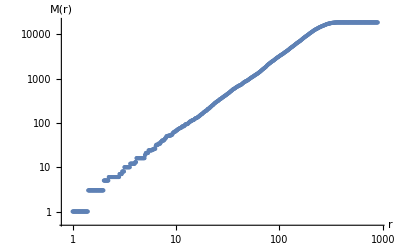

```mathematica
(*Para dado r0 cuento cuántas partículas hay en el círculo de tal radio*)
r0 = PowerRange[1,900,1.01];
n0 = ConstantArray[0,Length[r0]];
Do[
Do[
If[distancias⟦j⟧<r0⟦i⟧,n0⟦i⟧ = n0⟦i⟧ +1 ,break;]
,{j,1,Length[x]}];
,{i,1,Length[r0]}];

graphdata = ListLogLogPlot[Transpose[{r0,n0}],AxesLabel->{"r","M(r)"}]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.255505 | 0.00762568 | 33.5058 | 2.39731×10^-106
xfit | 1.69176 | 0.00229105 | 738.42 | 2.37517248589718×10^-516

0.255505+1.69176 xfit

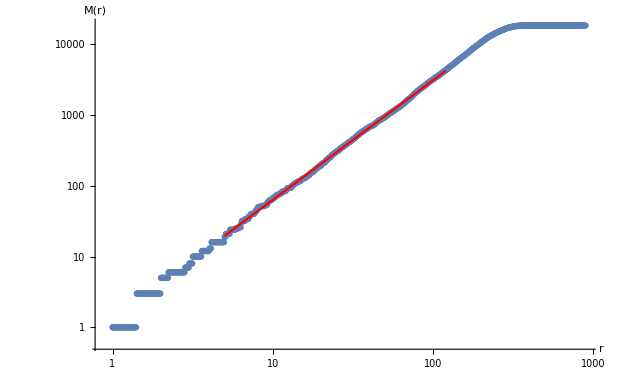

```mathematica
(*Ajuste lineal*)
(*Selecciono el rango de linealidad "a ojo" a partir del gráfico*)
triggerdown =5; (*valor mínimo de r*)
triggerup=120; (*valor máximo de r*)
linealr0 = {};
linealn0 = {};
Do[
If[r0⟦i⟧>triggerdown && r0⟦i⟧<triggerup,
AppendTo[linealr0,r0⟦i⟧];
AppendTo[linealn0, n0⟦i⟧];]
,{i,1,Length[r0]}
]
data = Log[Transpose[{linealr0,linealn0}]];
model=LinearModelFit[data,xfit,xfit];
model["ParameterTable"]
model["BestFit"] (*tengo que copiar a mano el modelo en la siguiente función*)
f[xfit_]:=0.25550462381836897+1.691756768294889 xfit
Mfit[rfit_]:=E^f[Log[rfit]];

graphfit = LogLogPlot[Mfit[r],{r,triggerdown,triggerup}, PlotStyle->Red];
Show[{graphdata, graphfit}]
```

```mathematica
(*Boxcounting*)
(*
Creo una matriz de tamaño Nmalla*Nmalla con las partículas atrapadas pintadas del número 1 y los lugares vacíos nulos (0);

Recorro todos los elementos de columna, si alguno es módulo Nbox significa que en ese elemento inclusive, termina una caja;
Entonces, si me paro en un elemento que no es módulo Nbox, veo si hay algún elemento en esa casilla y en las Nbox-1 debajo. Luego paso a la siguiente columna y repito el proceso;
Cuando me tope con la casilla módulo Nbox (final de la caja), veo si hay algún elemento en esa casilla y eln las N-box debajo, como antes y luego veo si la suma de casillas con partículas es mayor que cero;

En el medio meto la condición de que si la suma es > 1, salto a la siguiente caja;
Posteriormente, sigo el proceso en la caja de la derecha y luego en las de abajo.
*)
xnew = x+1; (*C++ inicia en 0, Mathematica en 1*)
ynew = y + 1;
malla = ConstantArray[0,{Nmalla,Nmalla}];
Do[
malla⟦xnew⟦j⟧,ynew⟦j⟧⟧=1;
,{j,1,Length[x]}]

Boxcounting[Nbox_, malla_,Nmalla_]:=Module[{suma,CantCajas,NuevaCaja},
suma = 0;
CantCajas = 0;
Do[
Do[
NuevaCaja = False;
If[Mod[j,Nbox]≠0,
Do[
suma = suma +malla⟦k,j⟧; 
,{k,i,i+Nbox-1}];,
Do[
suma = suma +malla⟦k,j⟧; 
,{k,i,i+Nbox-1}];
NuevaCaja = True;
];
If[NuevaCaja == True,
If[suma>0, CantCajas = CantCajas+1];
suma = 0;
]
,{j,1,Nmalla}];
,{i,1,Nmalla,Nbox}];
CantCajas
]

Nbox = PowerRange[1,Nmalla,2];
CantCajas = ConstantArray[0,Length[Nbox]];
resolution = ConstantArray[0,Length[Nbox]];
Do[
resolution⟦i⟧ = 1/Nbox⟦i⟧;
CantCajas⟦i⟧=Boxcounting[Nbox⟦i⟧,malla,Nmalla];
,{i,1,Length[Nbox]}]
```

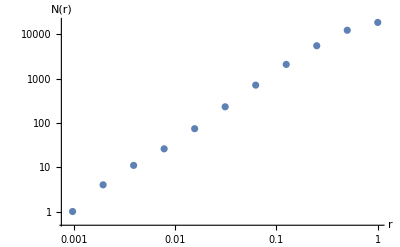

{1.,0.5,0.25,0.125,0.0625,0.03125,0.015625,0.0078125,0.00390625,0.00195313,0.000976563}

{18522,12350,5513,2091,712,231,74,26,11,4,1}

```mathematica
graphdata = ListLogLogPlot[Transpose[{resolution, CantCajas}], AxesLabel->{"r","N(r)"}]
Print[N[resolution]]
Print[CantCajas]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 10.7632 | 0.087924 | 122.415 | 6.89947×10^-10
xfit | 1.52975 | 0.023555 | 64.9436 | 1.63877×10^-8

10.7632+1.52975 xfit

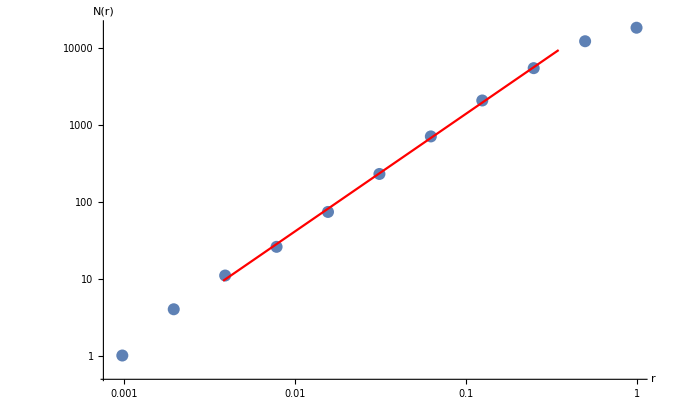

```mathematica
(*Ajuste lineal*)
(*Selecciono el rango de linealidad "a ojo" a partir del gráfico*)
triggerdown =0.0038; (*valor mínimo de r*)
triggerup=0.35; (*valor máximo de r*)
linealr0 = {};
linealn0 = {};
r0 = resolution;
n0 = CantCajas;
Do[
If[r0⟦i⟧>triggerdown && r0⟦i⟧<triggerup,
AppendTo[linealr0,r0⟦i⟧];
AppendTo[linealn0, n0⟦i⟧];]
,{i,1,Length[r0]}
]
data = Log[Transpose[{linealr0,linealn0}]];
model=LinearModelFit[data,xfit,xfit];
model["ParameterTable"]
model["BestFit"]
f[xfit_]:=10.763245273853029+1.5297473615927102xfit;
Mfit[rfit_]:=E^f[Log[rfit]];

graphfit = LogLogPlot[Mfit[r],{r,triggerdown,triggerup}, PlotStyle->Red];
Show[{graphdata, graphfit}]
```